```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
P[mm_,X_]:=Module[{x=X},
Return[LegendreP[mm,x]];
];
ψ[Ι_,J_,X_]:=Module[{i1=Ι,j1=J,xX=X},
nhs=2i1-1;
Return[Piecewise[{{√((2j1+1)/2)2^(k/2)P[j1,2^k xX-nhs],  (nhs-1)/2^k≤ xX && xX<(nhs+1)/2^k }},0]];
];
Ψ[X_]:=Module[{x=X},
Return[Flatten[Table[ψ[i,j,x],{i,1,2^(k-1)},{j,0,M-1}]]];
];
b[Ι_,X_]:=Module[{i=Ι,x=X},
Return[Piecewise[{{1, i h≤ x &&  x< (i+1)h}},0]];
];
B[X_]:=Module[{x=X},
Return[Table[b[i,x],{i,0,mh-1}]];
];
Φ[]:=Module[{},
Return[1/h Table[∫_0^1 Ψ[y]⟦i⟧B[y]⟦j⟧ⅆy,{i,1,mh},{j,1,mh}]];
];
ζ[Kk_,α_]:=Module[{kk=Kk},
Return[(kk+1)^(α+1)-2 kk^(α+1)+(kk-1)^(α+1)];
];
F[α_]:=Module[{},
A=IdentityMatrix[mh];
For[i=1,i< mh,i++,
For[j=i+1,j≤ mh,j++,
A⟦i,j⟧=ζ[j-i,α];
];
];
Return[h^α 1/Gamma[α+2] A];
];
P[α_]:=Module[{},
Return[Φ[].F[α].Inverse[Φ[]]];
];
𝔈[]:=Module[{},
Return[Simplify[𝒞[].P[α].Φ[]]];
];
𝒟[X_]:=Module[{x=X},
Aa=Table[Piecewise[{{∫_(jj/mh)^((jj+1)/mh) (B[s]⟦jj+1⟧)/(x-s)^β ⅆs ,jj/mh<x}},0],{jj,0,mh-1}];
Return[Aa];
];
(***************)
Dαf[X_]:=Module[{x=X},
Return[𝒞[].(Φ[].B[x])];
];
intABEL[X_]:=Module[{x=X},
Return[Subscript[λ, 1]*(𝔈[].𝒟[x])];
];
intUF[X_]:=Module[{x=X},
Return[Subscript[λ, 2]/mh*(𝔈[].Transpose[Φ[]].Transpose[U[]].Φ[].B[x])];
];
Gx[X_]:=Module[{x=X},
Return[G[].Φ[].B[x]];
];
(***************)
(*************************************)
α=0.25;Subscript[λ, 1]=1/2;Subscript[λ, 2]=1/3;β=1/2;
𝓊[x_,y_]=x-y;
ℊ[x_]=Gamma[3]/Gamma[2.75] x^1.75+Gamma[4]/Gamma[3.75] x^2.75-(√π x^(5/2)Gamma[3])/(2 Gamma[7/2])-(√π x^(7/2)Gamma[4])/(2 Gamma[9/2])-(7x)/36+3/20;
Ef[x_]=x^2+x^3;
M=2;
k=Input["enter k"];
(************************************)
n=2^(k-1);
nh=2n-1;
m=M-1;
mh=M(n-1)+m+1;
h=1/mh;
(**************var*************)
𝒞[]=Flatten[Table[c[i],{i,1,mh}]];
U[]=Table[u[i,j],{i,1,mh},{j,1,mh}];
G[]=Table[g[i],{i,1,mh}];
(**************var*************)
ΨΨ[x_]=Simplify[Φ[].B[x]];
For[i=0,i<mh,i++,Subscript[xx, i]=i/mh;];
```

```mathematica
gx=Simplify[Table[-ℊ[Subscript[xx, iu]]+G[].ΨΨ[Subscript[xx, iu]],{iu,0,mh-1}]];
G[]=Flatten[G[]/.Solve[gx==0,G[]]];
```

```mathematica
uxy=Simplify[Table[-𝓊[Subscript[xx, iu],Subscript[xx, ju]]+ΨΨ[Subscript[xx, iu]].U[].ΨΨ[Subscript[xx, ju]],{iu,0,mh-1},{ju,0,mh-1}]];
U[]=N[Partition[Flatten[Flatten[U[]]/.Solve[Flatten[uxy]==0,Flatten[U[]]]],mh]];
```

```mathematica
ODαf[x_]=Dαf[x];
OintABEL[x_]=intABEL[x];
OintUF[x_]=intUF[x];
OGx[x_]=Gx[x];
```

```mathematica
Answer=Table[Simplify[-ODαf[Subscript[xx, ou]]+OintABEL[Subscript[xx, ou]]+OintUF[Subscript[xx, ou]]+OGx[Subscript[xx, ou]]],{ou,0,mh-1}];
𝒞[]=Flatten[𝒞[]/.Solve[Answer==0,𝒞[]]];
```

```mathematica
f[x_]=Simplify[𝒞[].P[α].(ΨΨ[x])];
Print["f(x)= ",f[x]];
Print["************* M= ", M, "  ,k= ",k," *************"];
Print["LWM : ", Table[f[i/8],{i,0,7}]//MatrixForm]
```

f(x)= Piecewise[{{0., x≥1||x<0}, {0.0102729, 0≤x<1/16}, {0.0190159, 1/16≤x<1/8}, {0.0342483, 1/8≤x<3/16}, {0.0589628, 3/16≤x<1/4}, {0.0948547, 1/4≤x<5/16}, {0.143435, 5/16≤x<3/8}, {0.206146, 3/8≤x<7/16}, {0.284398, 7/16≤x<1/2}, {0.379583, 1/2≤x<9/16}, {0.493079, 9/16≤x<5/8}, {0.626256, 5/8≤x<11/16}, {0.780473, 11/16≤x<3/4}, {0.957082, 3/4≤x<13/16}, {1.15743, 13/16≤x<7/8}, {1.38284, 7/8≤x<15/16}, {1.63466, True}}]

************* M= 2  ,k= 4 *************

LWM : (0.0102729
0.0342483
0.0948547
0.206146
0.379583
0.626256
0.957082
1.38284)

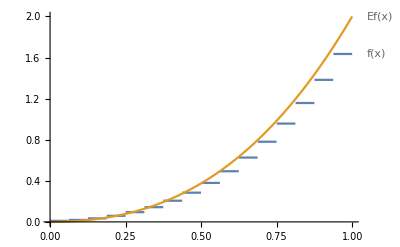

```mathematica
Plot[{f[x],Ef[x]},{x,0,1},PlotLabels-> "Expressions"]
```